```mathematica
(* ==========================================================================*)
(* analytic solution to the heat equation... *)
(* ... this can be compared to the numerical results to see if there's an effective
 perpendicular conductivity shape of the perturbation at time t=0 *)
sigma=0.15;

f0[x_]:=Exp[-(x-0.5)^2/(2*sigma^2)];

(*nth Fourier-Bessel coefficient of the initial condition*)
a[n_]:=With[{alpha=BesselJZero[0,n]//N},
(2/BesselJ[1,alpha]^2)*NIntegrate[x f0[x] BesselJ[0,alpha x],{x,0,1}]];

(*Fourier-Bessel expansion of the solution at time t*)
f[kappa_,t_]:=Table[With[{alpha=N[BesselJZero[0,n]]},
a[n] BesselJ[0,x alpha] Exp[-kappa alpha^2 t]],
{n,1,20}]//Total;
```

```mathematica
tcond=sigma^2/1.0
```

0.0225

```mathematica
p1=Plot[1 + 0.1f0[x],{x,0,1}];
```

```mathematica
p2=Plot[Evaluate[1 + 0.1f[1,0.5tcond]],{x,0,1},PlotStyle->Pink];
```

```mathematica
p3=Plot[Evaluate[1 + 0.1f[1,1tcond]],{x,0,1},PlotStyle->Green];
```

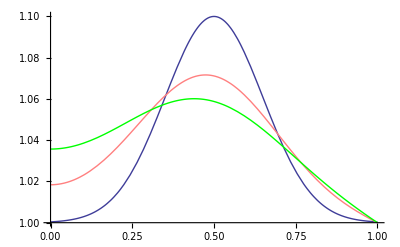

```mathematica
p4=Show[{p1,p2,p3}]
```

```mathematica
ClearAll[x]
```

```mathematica
centraltemp[t_]:=1+0.1f[1,t tcond]/.{x->0}
```

```mathematica
ts={0.0,0.05,0.1,0.5,1.0};
```

```mathematica
Map[centraltemp,ts]
```

{1.00046,1.00159,1.00286,1.01839,1.0357}

```mathematica
x=Range[0,100]/100.0;
```

```mathematica
y1=Map[1.0+0.1f0[#]&,x];
```

```mathematica
y2=1 + 0.1f[1,0.5tcond];
```

```mathematica
y3=1 + 0.1f[1,1.0tcond];
```

```mathematica
data=Transpose[{x,y1,y2,y3}];
```

```mathematica
Export["analytic.dat",
Append[Map[ToString[PaddedForm[#,{10,6}]]&,data,{2}],{}]];
```

```mathematica
myimport[file_]:=
Block[{data=Import["/Users/mike/Documents/ConductionTest/simulation-code/Athena-Cversion/bin/"<>file]},
data=Select[data,VectorQ[#,NumberQ]&];
data[[All,{2,3}]]]
```

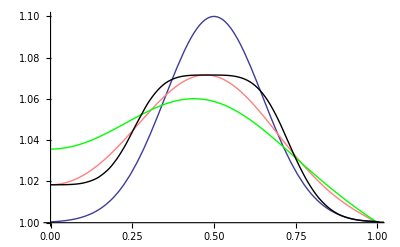

```mathematica
Show[{p4,
ListPlot[myimport["256-end.dat"],PlotStyle->Black,
Joined->True,
PlotRange->{1.0,1.1}]}]
```

```mathematica
data=Import["/Users/mike/Documents/ConductionTest/simulation-code/Athena-Cversion/bin/convergence.dat"];
data=Select[data,VectorQ[#,NumberQ]&];
```

```mathematica
data=Select[data,#[[3]]>0&];
```

```mathematica
x=data[[All,1]]*(sigma/2.0);
```

```mathematica
y=1.0/data[[All,3]];
```

```mathematica
data=Transpose[{Log[x],Log[y]}];
```

```mathematica
ClearAll[x,a,b]
```

```mathematica
nlm=NonlinearModelFit[Drop[data,1],a x+b,{a,b},x]
```

FittedModel[-1.44448-1.93562 x]

```mathematica
pad={{60,10},{40,10}};
```

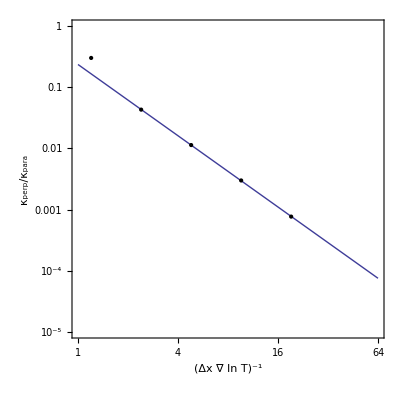

```mathematica
p=LogLogPlot[Exp[nlm[Log[x]]],
{x,1,64},
Epilog->{PointSize[Large],Point[data]},FrameLabel->{"(Δx ∇ ln T)^-1","κ_perp/κ_para"},
ImageSize->400,
AspectRatio->1,
Frame->True,
FrameLabel->{"r","T"},
ImagePadding->pad,
BaseStyle->{"FontSize"->14,"FontFamily"->"Helvetica"},
PlotRangePadding->None,
PlotRange->{10^-5,1},
FrameTicks->{{Automatic,None},{{1,2,4,8,16,32,64,128,256,512},None}}]
```

```mathematica
Exp[nlm[Log[4]]]
```

0.0161179

```mathematica
N[GoldenRatio]
```

1.61803